# Test Data Trace Plotting

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Sun 16 Feb 2014 18:44:22)

<<Set JLink` java stack size to 3072Mb>>

```mathematica
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

```mathematica
testDataFileDirectory = "V:\\docs\\k.VSDdata\\project.SPP\\Nlx\\SPP010\\2013-12-02_17-07-31";
```

```mathematica
(* FileNames[testDataFileDirectory<>"\\*"] *)
```

```mathematica
testFiles4=FileNames[testDataFileDirectory<>"\\Tet4*.ncs"]
```

{V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4a.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4b.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4c.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4d.ncs}

```mathematica
(*Methods[NN]*)
```

boolean equals(Object)
static nounou.FrameRange frames(int, int)
static nounou.FrameRange frames(int, int, int)
Class getClass()
static int get(int)
int hashCode()
static nounou.DataReader newReader()
void notify()
void notifyAll()
String toString()
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
$Reader = NN`newReader[]
```

«JavaObject[nounou.DataReader]»

```mathematica
$Reader@load[testFiles4]
```

```mathematica
$Reader@dataSummary[]
```

DataReader loaded data summary:
     header : XHeaderNull
     data   : XData(4 channels, 1 segments, with lengths Vector(151597056), fs=32000.0)
     dataAux: XDataNull
     layout : XLayoutNull
     mask   : XMaskNull
     events : XEventsNull
     spikes : XSpikesNull

```mathematica
151597056/16
```

9474816

```mathematica
151597056/16/10.
```

947482.

```mathematica
$Reader@dataDecimate[]@readTrace[0, NN`frames[0, 20000,10], 0]@length[]
```

2001

```mathematica
Length[$Reader@readTrace[0, NN`frames[0,5000,10], 0]]
```

501

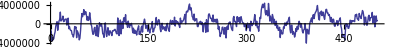

```mathematica
grOri=ListLinePlot[$Reader@readTrace[0, NN`frames[0,5000,10], 0],AspectRatio->1/10]
```

```mathematica
$Reader@data[]@sampleRate[]
```

2000.

```mathematica
$Reader@setFilterHz[0,1000]
```

```mathematica
$Reader@dataFIR[]@kernel[] == Null
```

True

```mathematica
$Reader@setFilterHz[0.5,20]
```

```mathematica
$Reader@dataFIR[]@toString[]
```

XDataFilterFIR: kernel class breeze.signal.support.FIRKernel1D multiplier: 256: FIRKernel1D(firwin): 1024 taps, DenseVector(5.0E-4, 0.02), Hamming window (0.54, 0.46), zeroPass=false, nyquist=1.0, scale=true, multiplier: 256

```mathematica
Length[$Reader@readTrace[0, NN`frames[0,5000,10], 0]]
```

501

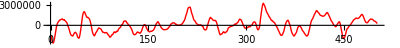

```mathematica
grFilt=ListLinePlot[$Reader@readTrace[0, NN`frames[0, 5000,10], 0],AspectRatio->1/10,PlotStyle->Red]
```

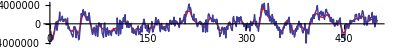

```mathematica
Show[grFilt,grOri,PlotRange->All]
```

```mathematica
$Reader@dataFIR[]@readTrace[0, NN`frames[0, 5000,10], 0]
```

«JavaObject[scala.collection.immutable.Vector]»

```mathematica
$Reader@dataFIR[]@readTrace[0, NN`frames[0, 5000,10], 0]
```

```mathematica
$Reader@dataFIR[]@readTrace[0, NN`frames[0, 5000,10], 0]@toString[]
```

Vector(-690008860)